```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
f[x_,a1_,a2_,a3_,a4_]:=a1  + a2 x + a3 x^2 + a4 x^4
```

```mathematica
fSolve[a1_,a3_]:=Block[{sol=NSolve[{f[1,a1,a,a3,b]==1,f[2,a1,a,a3,b]==3},{a,b}]},sol[[1,All,2]]]
fSolver[a1_,a3_]:=Block[{sol=fSolve[a1,a3]},f[x,a1,sol[[1]],a3,sol[[2]]]]
```

```mathematica
sol1=fSolver[1,2];
sol2=fSolver[0,1];
sol3=fSolver[-3,1];
sol4=fSolver[3,1];
```

```mathematica
Needs["PolygonPlotMarkers`"]

allShapes=PolygonMarker[All]
Tooltip[Graphics[{FaceForm[Hue@Random[]],EdgeForm[{Black,Thickness[0.003],JoinForm["Miter"]}],PolygonMarker[#,1]},ImageSize->30,PlotRange->1.5,PlotRangePadding->0,ImagePadding->0],#]&/@allShapes
```

{TripleCross,Y,UpTriangle,UpTriangleTruncated,DownTriangle,DownTriangleTruncated,LeftTriangle,LeftTriangleTruncated,RightTriangle,RightTriangleTruncated,ThreePointedStar,Cross,DiagonalCross,Diamond,Square,FourPointedStar,DiagonalFourPointedStar,FivefoldCross,Pentagon,FivePointedStar,FivePointedStarThick,SixfoldCross,Hexagon,SixPointedStar,SixPointedStarSlim,SevenfoldCross,SevenPointedStar,SevenPointedStarNeat,SevenPointedStarSlim,EightfoldCross,Disk,H,I,N,Z,S,Sw,Sl}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

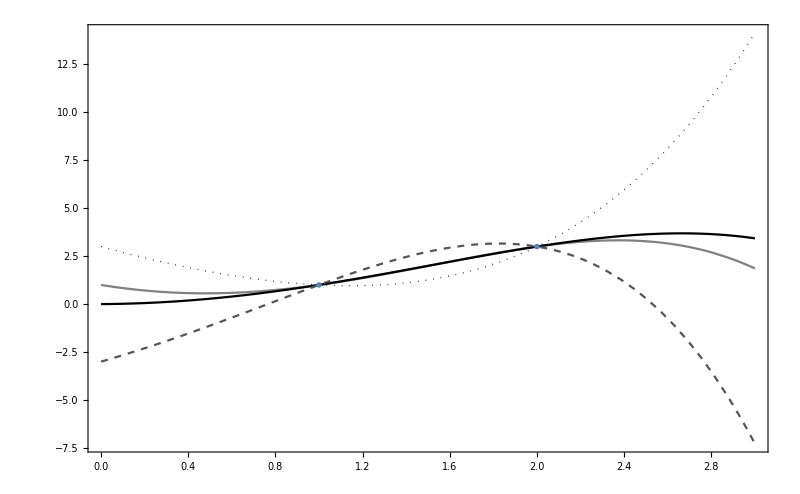

```mathematica
Show[Plot[{sol1,sol2,sol3,sol4},{x,0,3},Axes->None,PlotStyle->{Gray,Black,Directive[Darker@Gray,Dashed],Directive[Black,Dotted,Thick]},PlotRange->Full,FrameLabel->None,ImageSize->800,FrameTicks->None,FrameStyle->Directive[Black,16,Thick],Frame->{True,True,False,False},PlotStyle->"Brighband}1"],ListPlot[{{1,1},{2,3}},PlotMarkers->Graphics[{FaceForm[Blue],PolygonMarker[ToString@"Disk",Scaled[0.04]]},AlignmentPoint->{0,0}]]]
```

## Better

```mathematica
fSolve1[a1_,a3_,a4_]:=Block[{sol=NSolve[{f[1,a1,a,a3,a4]==1},{a}]},sol[[1,All,2]]]
fSolver1[a1_,a3_,a4_]:=Block[{sol=fSolve1[a1,a3,a4]},f[x,a1,sol[[1]],a3,a4]]
```

```mathematica
sol1a=fSolver1[4,0,0];
sol2a=fSolver1[8,1,0];
sol3a=fSolver1[0,1,0];
sol4a=fSolver1[-4,-1,0];
sol5a=fSolver1[-5,0,0];
sol6a=fSolver1[7,0,0];
```

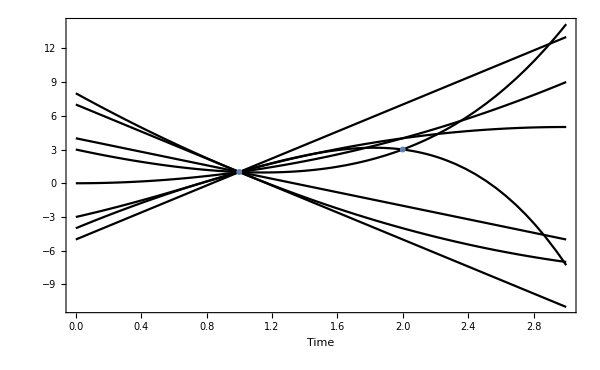

```mathematica
g2=Show[Plot[{sol3, sol4,sol1a,sol2a,sol3a,sol4a,sol5a,sol6a},{x,0,3},Axes->None,PlotStyle->Black,PlotRange->Full,FrameLabel->{"Time",None,None,"Output"},ImageSize->600,FrameTicks->None,FrameStyle->Directive[Black,20,Thick],Frame->{True,False,False,True},PlotStyle->"Brighband}1"],ListPlot[{{2,3}},PlotMarkers->Graphics[{FaceForm[Blue],PolygonMarker[ToString@"Disk",Scaled[0.08]]},AlignmentPoint->{0,0}]],
ListPlot[{{1,1}},PlotMarkers->Graphics[{FaceForm[Orange],PolygonMarker["DownTriangle",Scaled[0.08]]},AlignmentPoint->{0,0}]]]
```

```mathematica
g1=Show[ListPlot[{{2,2}},PlotStyle->Opacity[1,White],PlotRange->{{0,7},{0,7}},FrameLabel->{"θ_1","θ_2"},ImageSize->600,FrameTicks->None,FrameStyle->Directive[Black,20,Thick],Frame->{True,True,False,False}],Graphics[{Orange,FilledCurve[BezierCurve[{{1,1},{2,3.5},{4,1},{6,3},{5,7},{4,8},{2,5},{1,1}}]]}],Graphics[{Blue,FilledCurve[BezierCurve[{{6,1},{7.5,2},{6.5,3},{6.1,1.5}}]]}]]
```

-Graphics-

```mathematica
gFinal=GraphicsRow[{g1,g2}]
```

-Graphics-

## Can be improved still

```mathematica
sol1a=fSolver1[4,0,0];
sol2a=fSolver1[5,1,0];
sol3a=fSolver1[0,1,0];
sol4a=fSolver1[-4,-1,0];
sol5a=fSolver1[-5,0,2];
sol6a=fSolver1[-3,0,-1];
sol7a=fSolver1[-2,-2,1];
sol8a=fSolver1[-1.5,2,1];
```

```mathematica
fSolve2[a1_,a3_,a4_]:=Block[{sol=NSolve[{f[1,a1,a,a3,a4]==-5},{a}]},sol[[1,All,2]]]
fSolver2[a1_,a3_,a4_]:=Block[{sol=fSolve2[a1,a3,a4]},f[x,a1,sol[[1]],a3,a4]]
sol1b=fSolver2[-3,-1,0];
sol2b=fSolver2[-6,0,2];
```

```mathematica
sol1b/.x->1
```

-5.

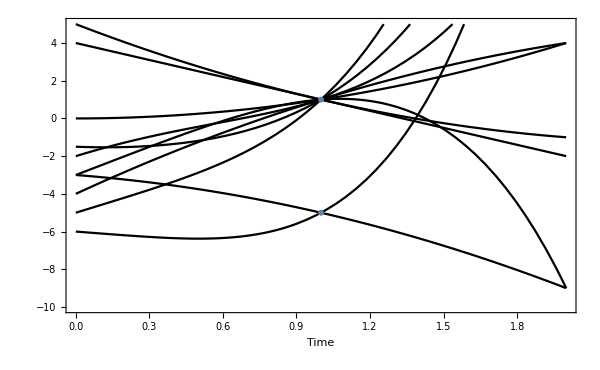

```mathematica
g2=Show[Plot[{sol1a,sol2a,sol3a,sol4a,sol5a,sol6a,sol7a,sol8a,sol1b,sol2b},{x,0,2},Axes->None,PlotStyle->Black,PlotRange->{Full,{-10,5}},FrameLabel->{"Time",None,None,"Output"},ImageSize->600,FrameTicks->None,FrameStyle->Directive[Black,20,Thick],Frame->{True,False,False,True},PlotStyle->"Brighband}1"],ListPlot[{{1,-5}},PlotMarkers->Graphics[{FaceForm[Blue],PolygonMarker[ToString@"Disk",Scaled[0.08]]},AlignmentPoint->{0,0}]],
ListPlot[{{1,1}},PlotMarkers->Graphics[{FaceForm[Orange],PolygonMarker["DownTriangle",Scaled[0.08]]},AlignmentPoint->{0,0}]]]
```

```mathematica
gFinal=GraphicsRow[{g1,g2}]
```

-Graphics-

```mathematica
Export["../figures/contour_volumes1.pdf",gFinal]
```

../figures/contour_volumes.pdf